```mathematica
SetDirectory[NotebookDirectory[]];
Get["betas.m"];
```

## Different loops if running from single point

```mathematica
{Black, Darker[RGBColor[1,0.25,0.75],0.15],Darker[Blue,0.1],Darker[Orange,0.2],Darker[Red,0.25], Darker[Cyan,0.3],Darker[Green,0.4]}
```

{GrayLevel[0],RGBColor[0.85, 0.2125, 0.6375],RGBColor[0., 0., 0.9],RGBColor[0.8, 0.4, 0.],RGBColor[0.75, 0., 0.],RGBColor[0., 0.7, 0.7],RGBColor[0., 0.6, 0.]}

```mathematica
ClearAll@loopColor;
{loopColor[1,1,1,1,1,1],loopColor[2,2,2,2,2,2],loopColor[3,3,3,3,3,3],loopColor[3,3,3,2,2,1],loopColor[4,4,4,3,3,2],loopColor[3,3,3,2,2,2],loopColor[4,4,4,3,3,3]}={Black, Darker[RGBColor[1,0.25,0.75],0.1],Darker[Blue,0.1],Darker[Orange,0.2],Darker[Red,0.25], Darker[Cyan,0.3],Darker[Green,0.4]};
drawSolutions[cons_,{tmin_,tmax_},init_]:=(*cons_ of form {{3,3,3,2,2,1},{...},...}*)
Plot[
Evaluate[Table[
z[t]/.
NDSolve[
{x1'[t]==((x1dot@@cons[[i]])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot@@cons[[i]])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot@@cons[[i]])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot@@cons[[i]])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot@@cons[[i]])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot@@cons[[i]])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==init[[1]],x2[0]==init[[2]],x3[0]==init[[3]],y1[0]==init[[4]],y2[0]==init[[5]],z[0]==init[[6]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,tmin,tmax}][[1,6]],
{i,1,Length@cons}
]],
{t,tmin,tmax},
PlotStyle->Table[loopColor@@cons[[i]],{i,1,Length@cons}],PlotLegends->Table["|"<>ToString@cons[[i,1]]<>","<>ToString@cons[[i,2]]<>","<>ToString@cons[[i,3]]<>"|"<>ToString@cons[[i,4]]<>","<>ToString@cons[[i,5]]<>"|"<>ToString@cons[[i,6]]<>"|",{i,1,Length@cons}], FrameLabel->{"t","z"},ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True
]
drawSolutions[cons_,{tmin_,tmax_}]:=(*cons_ of form {{{3,3,3,2,2,1},{x10,x20,x30,y10,y20,z0}},{...},...}*)
Plot[
Evaluate[Table[
z[t]/.
NDSolve[
{x1'[t]==((x1dot@@cons[[i,1]])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot@@cons[[i,1]])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot@@cons[[i,1]])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot@@cons[[i,1]])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot@@cons[[i,1]])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot@@cons[[i,1]])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==cons[[i,2,1]],x2[0]==cons[[i,2,2]],x3[0]==cons[[i,2,3]],y1[0]==cons[[i,2,4]],y2[0]==cons[[i,2,5]],z[0]==cons[[i,2,6]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,tmin,tmax}][[1,6]],
{i,1,Length@cons}
]],
{t,tmin,tmax},
PlotStyle->Table[loopColor@@cons[[i,1]],{i,1,Length@cons}],PlotLegends->Table["|"<>ToString@cons[[i,1,1]]<>","<>ToString@cons[[i,1,2]]<>","<>ToString@cons[[i,1,3]]<>"|"<>ToString@cons[[i,1,4]]<>","<>ToString@cons[[i,1,5]]<>"|"<>ToString@cons[[i,1,6]]<>"|",{i,1,Length@cons}], FrameLabel->{"t","z"},ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True
]
```

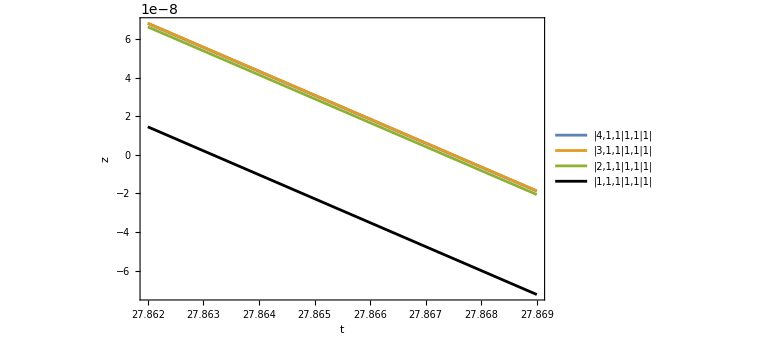

figures/x1contribution1.pdf

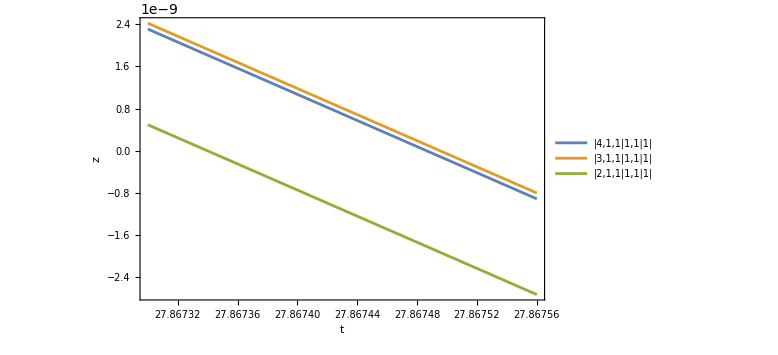

figures/x1contribution2.pdf

```mathematica
drawSolutions[{{4,1,1,1,1,1},{3,1,1,1,1,1},{2,1,1,1,1,1},{1,1,1,1,1,1}},{27.862,27.869},{x10,x20,x30,y10,y20,z0}/.expdata]
Export["figures/x1contribution1.pdf",%]
drawSolutions[{(*{1,1,1,1,1,1},*){4,1,1,1,1,1},{3,1,1,1,1,1},{2,1,1,1,1,1}},{27.8673,27.86756},{x10,x20,x30,y10,y20,z0}/.expdata]
Export["figures/x1contribution2.pdf",%]
```

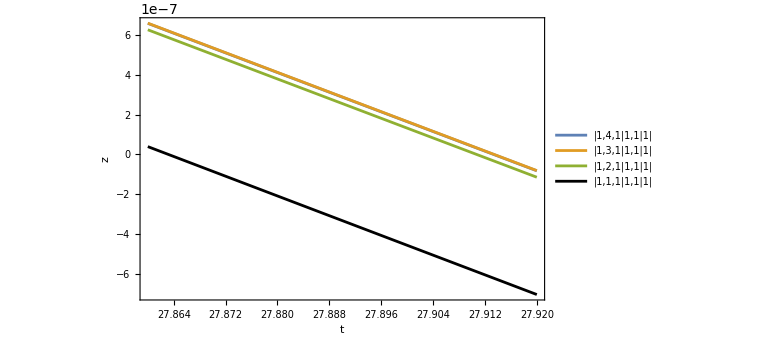

figures/x2contribution1.pdf

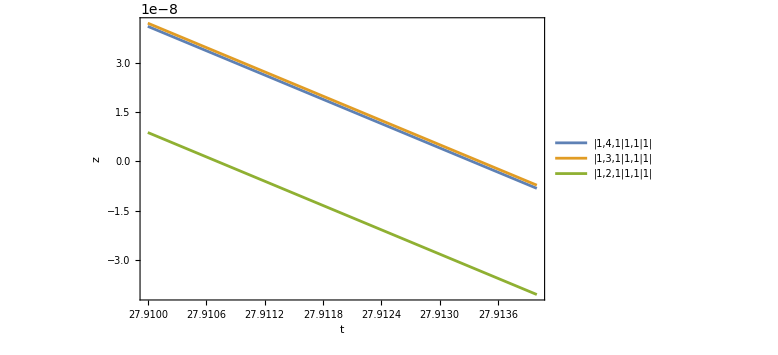

figures/x2contribution2.pdf

```mathematica
drawSolutions[{{1,4,1,1,1,1},{1,3,1,1,1,1},{1,2,1,1,1,1},{1,1,1,1,1,1}},{27.86,27.92},{x10,x20,x30,y10,y20,z0}/.expdata]
Export["figures/x2contribution1.pdf",%]
drawSolutions[{{1,4,1,1,1,1},{1,3,1,1,1,1},{1,2,1,1,1,1}},{27.91,27.914},{x10,x20,x30,y10,y20,z0}/.expdata]
Export["figures/x2contribution2.pdf",%]
```

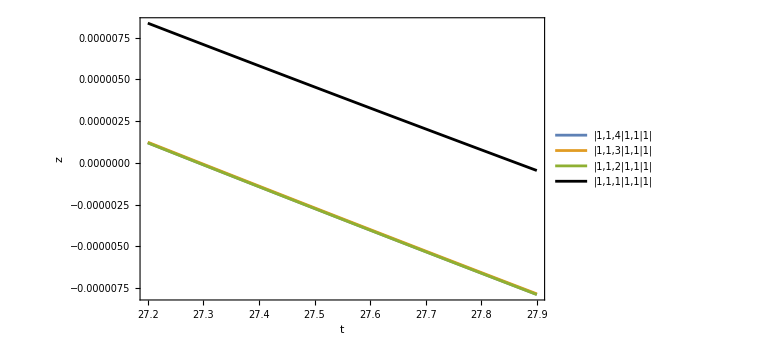

figures/x3contribution1.pdf

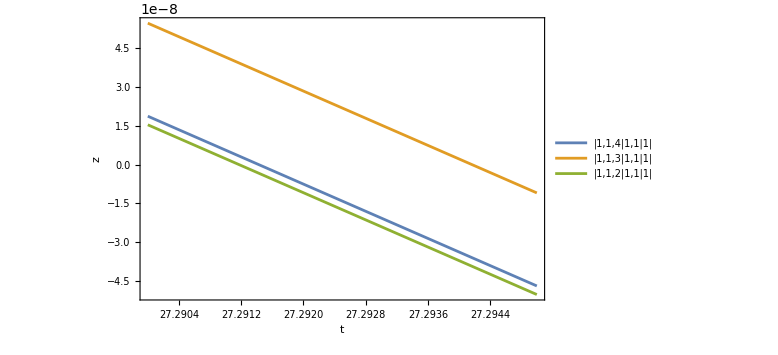

figures/x3contribution2.pdf

```mathematica
drawSolutions[{{1,1,4,1,1,1},{1,1,3,1,1,1},{1,1,2,1,1,1},{1,1,1,1,1,1}},{27.2,27.9},{x10,x20,x30,y10,y20,z0}/.expdata]
Export["figures/x3contribution1.pdf",%]
drawSolutions[{{1,1,4,1,1,1},{1,1,3,1,1,1},{1,1,2,1,1,1}},{27.29,27.295},{x10,x20,x30,y10,y20,z0}/.expdata]
Export["figures/x3contribution2.pdf",%]
```

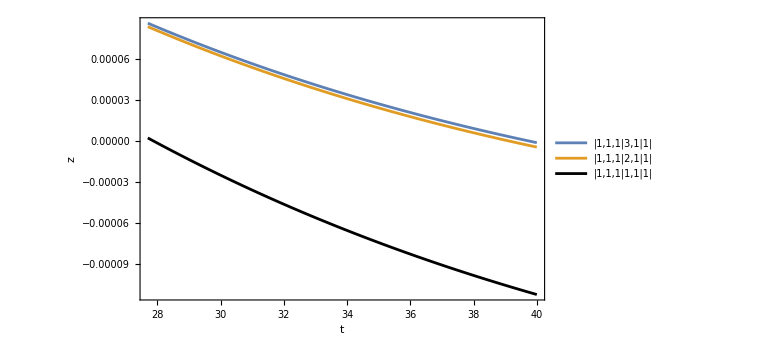

figures/y1contribution.pdf

```mathematica
drawSolutions[{{1,1,1,3,1,1},{1,1,1,2,1,1},{1,1,1,1,1,1}},{27.7,40},{x10,x20,x30,y10,y20,z0}/.expdata]
Export["figures/y1contribution.pdf",%]
```

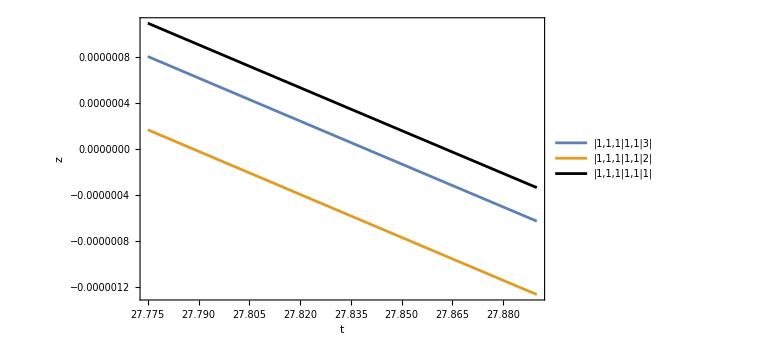

figures/zcontribution.pdf

```mathematica
drawSolutions[{{1,1,1,1,1,3},{1,1,1,1,1,2},{1,1,1,1,1,1}},{27.775,27.89},{x10,x20,x30,y10,y20,z0}/.expdata]
Export["figures/zcontribution.pdf",%]
```

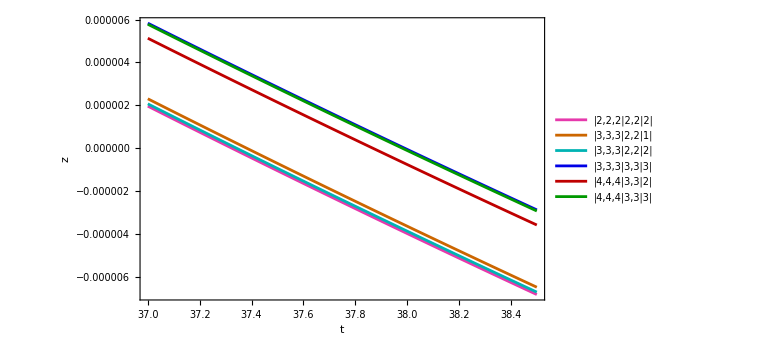

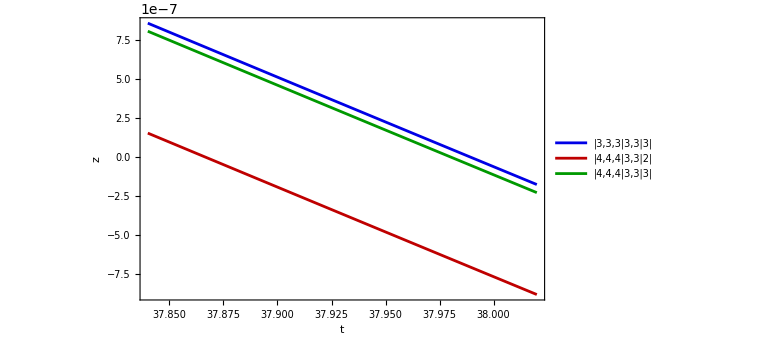

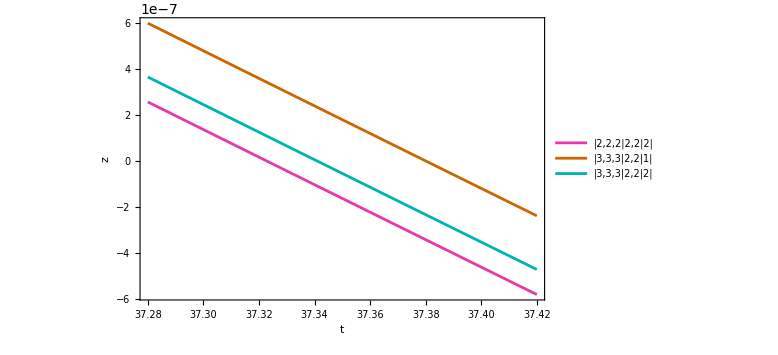

```mathematica
drawSolutions[{{2,2,2,2,2,2},{3,3,3,2,2,1},{3,3,3,2,2,2},{3,3,3,3,3,3},{4,4,4,3,3,2},{4,4,4,3,3,3}},{37,38.5},{x10,x20,x30,y10,y20,z0}/.expdata]
drawSolutions[{{3,3,3,3,3,3},{4,4,4,3,3,2},{4,4,4,3,3,3}},{37.84,38.02},{x10,x20,x30,y10,y20,z0}/.expdata]
drawSolutions[{{2,2,2,2,2,2},{3,3,3,2,2,1},{3,3,3,2,2,2}},{37.28,37.42},{x10,x20,x30,y10,y20,z0}/.expdata]
```